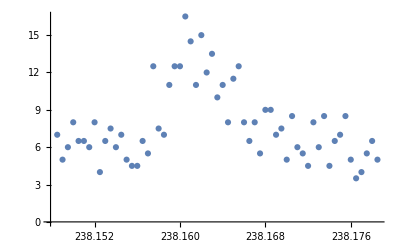

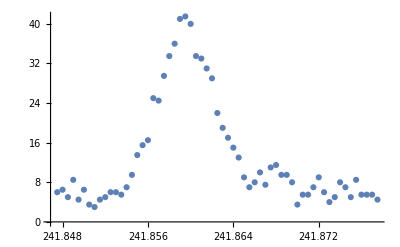

{a→7.59927,b→238.162,c→0.00367265,d→6.19776}

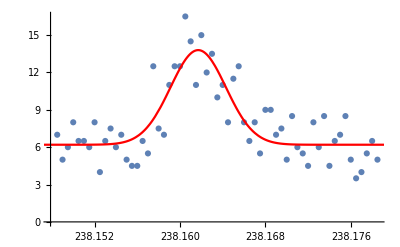

{a→33.2865,b→241.86,c→0.00354536,d→6.28945}

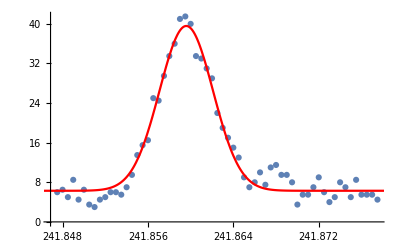

13.797

39.576

0.535205

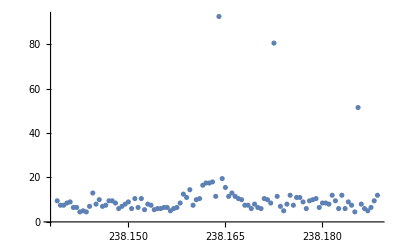

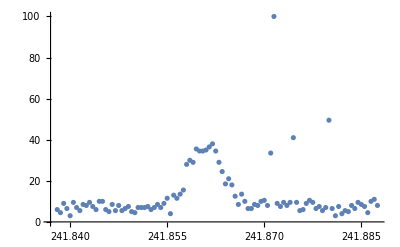

{a→88.2352,b→238.164,c→0.000286082,d→9.92767}

General::munfl: Exp[-7681.06] is too small to represent as a normalized machine number; precision may be lost.

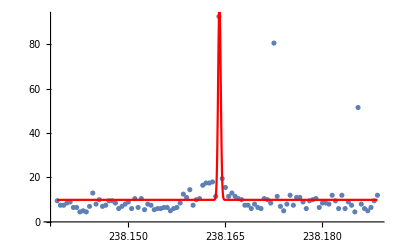

{a→28.3907,b→241.861,c→0.00320011,d→9.83432}

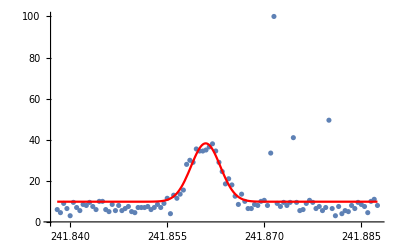

38.2251

-1.63775

```mathematica
DirName = "D:\\Document\\Seafile\\Experiment\\Artiq\\Sequence\\repository\\data\\2021-04-16-23-38\\";
FileName = "15000.0us.csv";
FullFile = DirName <> FileName;
data = Transpose[Import[FullFile]];
redband = Transpose[{data[[1]],(200-data[[2]])/2}];
blueband = Transpose[{data[[3]],(200-data[[4]])/2}];
redband = redband[[Range[20,80,1]]];
blueband = blueband[[Range[20,80,1]]];
ListPlot[redband,PlotRange->Full]
ListPlot[blueband,PlotRange->Full]
expr = a*Exp[-(x-b)^2/c^2]+d;
redfit = FindFit[redband,expr,{{a,30},{b,238.163},{c,0.015},{d,5}},x,MaxIterations->10000]
Show[ListPlot[redband,PlotRange->Full],Plot[expr/.redfit,{x,Min[data[[1]]],Max[data[[1]]]},PlotRange->Full,PlotStyle->Red]]
bluefit = FindFit[blueband,expr,{{a,30},{b,241.865},{c,0.015},{d,5}},x,MaxIterations->10000]
Show[ListPlot[blueband,PlotRange->Full],Plot[expr/.bluefit,{x,Min[data[[3]]],Max[data[[3]]]},PlotRange->Full,PlotStyle->Red]]
red = a+d/.redfit
blue = a+d/.bluefit
number = red/(blue-red)
```